## Integral de Linea (Cambio de variable)

```mathematica
z=(1/2)*Exp[I*θ];
dz=D[z,θ];
Integrate[(1/((z^2)(z-I)))*dz,{θ,0,2*Pi}]
```

2 ⅈ π

```mathematica
ClearAll["Global`*"]
```

```mathematica
Abs[z-2I]==3/2
```

```mathematica
Abs[-2 ⅈ+(x+I*y)]==3/2//ComplexExpand
```

√(x^2+(-2+y)^2)==3/2

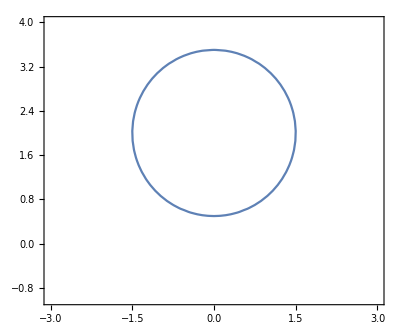

```mathematica
ContourPlot[√(x^2+(-2+y)^2)==3/2,{x,-3,3},{y,-1,4},Axes->True,AspectRatio->Automatic]
```

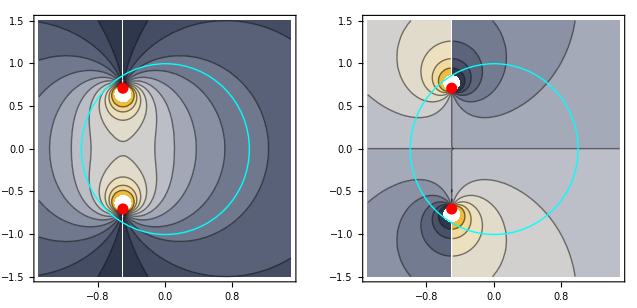

```mathematica
With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},GraphicsRow[Table[ContourPlot[g[1/Sqrt[4 (x+I y-z1) (x+I y-z2)]],{x,-1.5,1.5},{y,-1.5,1.5},ColorFunction->"GrayYellowTones",Epilog->{Cyan,Thick,Circle[{0,0}],Red,PointSize[0.02],Point[{Re@#,Im@#}&/@{z1,z2}]},Contours->11],{g,{Re,Im}}]]]
```